## Star - Disk magnetic field interaction

### Setup

```mathematica
$HistoryLength=0;ClearAll["Global`*"];
```

```mathematica
rloglog[functions_,yLabel_,legendLabels_,coords_]:=LogLogPlot[functions, {r,rMin,rMax}, Frame->True,FrameLabel->{"r (AU)", yLabel},ImageSize->Large,PlotLegends->legendLabels,BaseStyle->{FontWeight->"Bold",FontSize->14},PlotRange->Full, GridLines->coords]
au=1.5*10^13;
G=6.67*10^-8;
Msun=2*10^33;
Mstar=1*Msun;
year=3.15*10^7;
rMin=r0star;
rMax=10;
```

### Stellar field

```mathematica
B0star = 1000; (* typical polar field at the sun's surface is about 1 gauss, more like 1000 gauss for t-tauri *)
r0star=0.01; (* 1/200 of an AU is roughly photosphere *)
Bstar[r_]:=B0star*(r/r0star)^-3 (* dipole falloff *)
```

### MMSN model

```mathematica
(* input r is in au, other quantities are in cm *)
r0disk=1;
cs=0.6 * 10^5 ;(* from phil's book, cs at 1 au is 0.6 km/s, not a strong function of r *)
hor=0.02; (* h/r is not a strong function of r, constant is probably ok *)
Σ[r_]:=1.7 * 10^3 * (r/r0disk)^(-3/2); (* MMSN*10 in g/cm^2, r in AU *)
h[r_]:=hor*r; (* scale height in au *)
ρ[r_]:=1/(√(2π))Σ[r]/(h[r]*au);
P[r_]:=ρ[r]*cs^2;
```

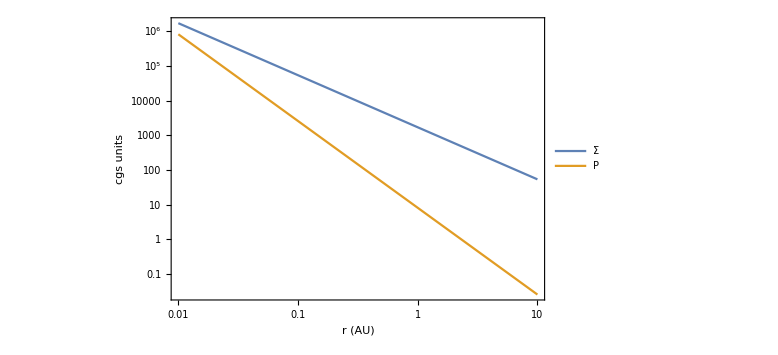

```mathematica
rloglog[{Σ[r],P[r]}, "cgs units",{"Σ","P"},{{},{}}]
```

### Randomly oriented disk field

```mathematica
βrand[r_]:= 10^5; (* complete guess *)
Brand[r_]:=√(βrand[r]^-1*P[r])
```

### Net disk field (without star influence)

```mathematica
(* this is harder *)
Bnet0=Brand[1];
n=0.5;
Bnet[r_]:=Bnet0*(r/r0disk)^-n
```

```mathematica
Bnet[1]
```

2.85279 √(1/βrand0)

### Plot of fields

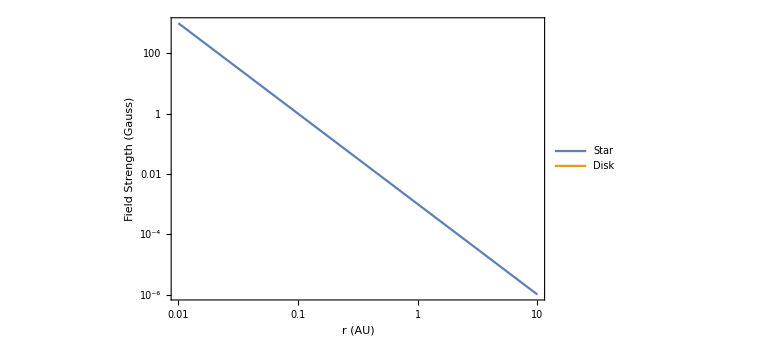

```mathematica
rloglog[{Bstar[r],Bnet[r]}, "Field Strength (Gauss)",{"Star","Disk"},{{},{}}]
```

### Find equal B radius

```mathematica
rEqB=Solve[Bstar[r]==Bdisk[r],r,Reals][[1,1,2]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

1/r^3

### Stellar co-rotation

```mathematica
periodStar=7/365;
Ωstar[r_]:=2π periodStar^-1
```

### Disk rotation

```mathematica
period0disk=1.0;
Ωdisk[r_]:=2π*period0disk^-1*(r/r0disk)^(-3/2)
tdisk[r_]:=2*π*Ωdisk[r]^-1
```

### Plot of rotations

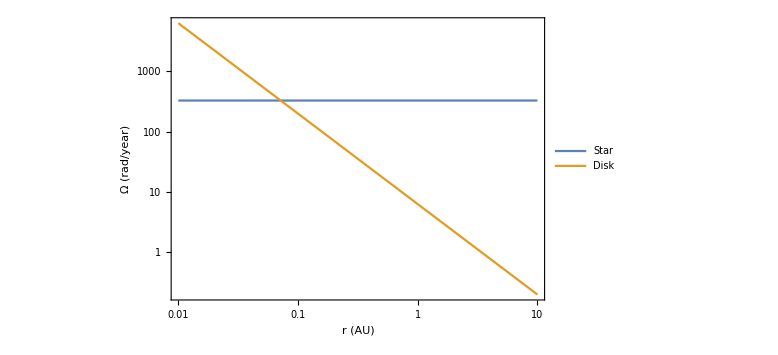

```mathematica
rloglog[{Ωstar[r],Ωdisk[r]},"Ω (rad/year)",{"Star","Disk"},{{},{}}]
```

### Find co-rotation radius

```mathematica
rCoRot=Solve[Ωstar[r]==Ωdisk[r],r][[1,1,2]]
```

0.0716479

### magnetosphere radius (stellar field removes angular momentum on the same time-scale as viscous evolution)

```mathematica
α=0.01;
tadv[r_]:=tdisk[r]/(α*hor0);
tmagTorque[r_]:=(2π Σ[r] √(G Mstar (r*au)))/(Bstar[r]^2*(r*au))/year
```

```mathematica
tadv[1]
```

100./hor0

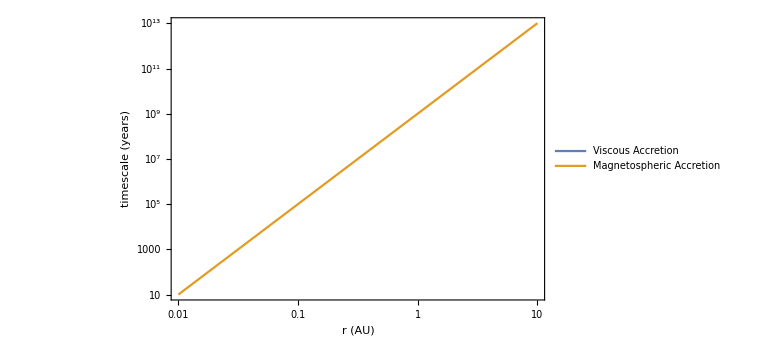

```mathematica
rloglog[{tadv[r],tmagTorque[r]}, "timescale (years)",{"Viscous Accretion","Magnetospheric Accretion"},{{},{}}]
```

```mathematica
rMS = Solve[tmagTorque[r]==tadv[r],r][[4,1,2]]
```

(0.000487576-0.0015006 ⅈ)/hor0^(2/5)

```mathematica
rMS=((3 B0star^2(r0star*au)^6)/(2*(10^-8*Mstar/year)*√(G*Mstar)))^(2/7)/au   (* from Phil's book *)
rMS/(1/200)
```

0.0848914

16.9783

### Summary of important radii

```mathematica
r0star
rCoRot
rMS
rEqB
```

0.01

0.0716479

0.0848914

1/r^3

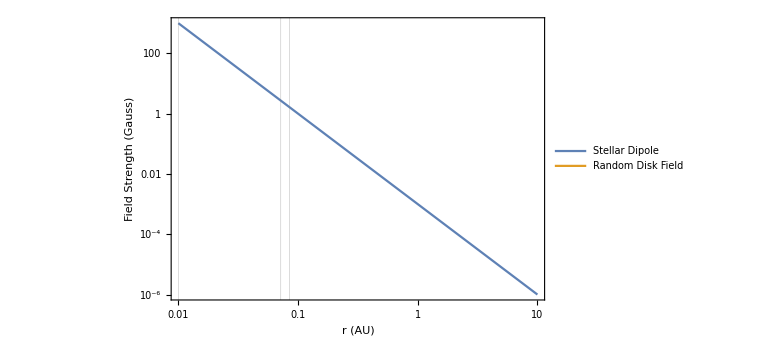

```mathematica
rloglog[{Bstar[r],Bdisk[r]},"Field Strength (Gauss)",{"Stellar Dipole","Random Disk Field"},{{r0star,rCoRot,rMS,rEqB},{}}]
```

### Time scale for the stellar field to pass through an entire annulus (should there be an alpha in here?)

```mathematica
tDeposit[r_]:=α^-1(Ωstar[r]-Ωdisk[r])^-1
```

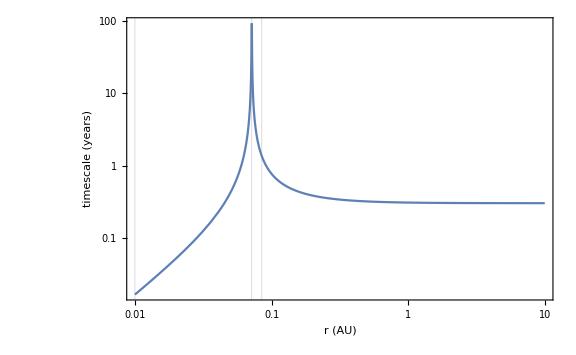

```mathematica
rloglog[{Abs[tDeposit[r]]}, "timescale (years)",{""},{{r0star,rCoRot,rMS,rEqB},{}}]
```

### Rate at which field will deposit into the disk (mostly just multiply previous by stellar field strength)

```mathematica
fieldIntoDiskPerYearDr[r_]:=1/tDeposit[r]*(Bstar[r])
```

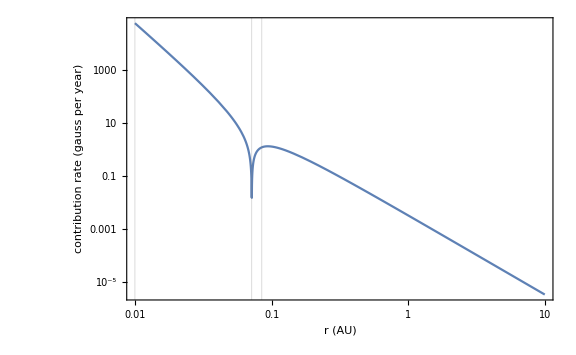

```mathematica
rloglog[{Abs[fieldIntoDiskPerYearDr[r]]}, "contribution rate (gauss per year)",{""},{{r0star,rCoRot,rMS,rEqB},{}}]
```

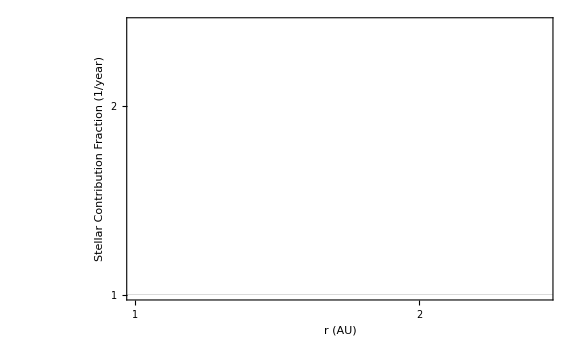

```mathematica
rloglog[{Abs[fieldIntoDiskPerYearDr[r]/Bdisk[r]]}, "Stellar Contribution Fraction (1/year)",{""},{{r0star,rCoRot,rMS,rEqB},{1.0}}]
```

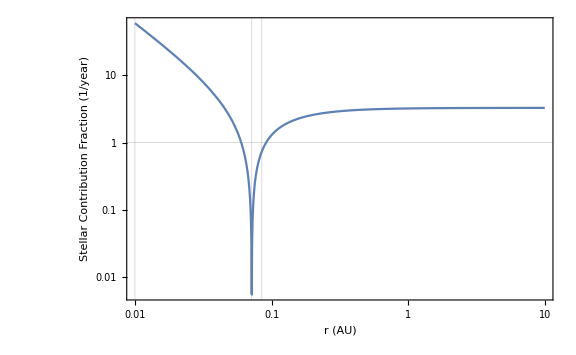

```mathematica
rloglog[{Abs[fieldIntoDiskPerYearDr[r]/Bstar[r]]}, "Stellar Contribution Fraction (1/year)",{""},{{r0star,rCoRot,rMS,rEqB},{1.0}}]
```

```mathematica
totalFluxIntoDiskPerYear=∫_rMS^rEqB fluxIntoDiskPerYearDr[r]ⅆr
totalFluxInDiskToStart=∫_rMS^1 diskFluxDr[r]ⅆr
totalFluxInDiskToStart/totalFluxIntoDiskPerYear
```

∫_0.0848914^(1/r^3) fluxIntoDiskPerYearDr[r]ⅆr

∫_0.0848914^1 diskFluxDr[r]ⅆr

(∫_0.0848914^1 diskFluxDr[r]ⅆr)/(∫_0.0848914^(1/r^3) fluxIntoDiskPerYearDr[r]ⅆr)

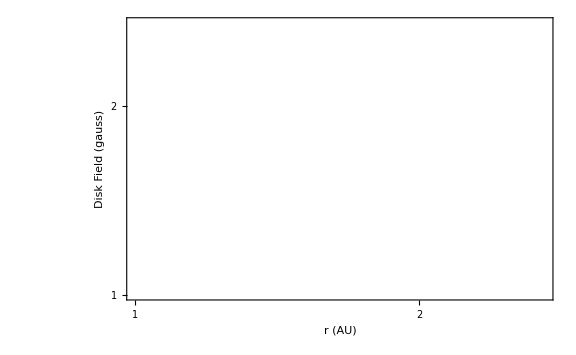

```mathematica
rloglog[Table[Bdisk[r]+i*fieldIntoDiskPerYearDr[r],{i,0,6}], "Disk Field (gauss)","",{{r0star,rCoRot,rMS,rEqB},{}}]
```

```mathematica
1/0.07
```

14.2857